## Cria uma lista dos valores cobrados pelos produtos que obtiveram máximo lucro individual, isto feito para toda a faixa de lucro percentual (10% a 300%)

```mathematica
dir = "C:\\Users\\sucod\\OneDrive\\Lenovo\\Documentos\\Sql";
ListaValorMaxLucro = {0};

For[i=0,i<300,i+=10;
imp = Import[dir<>"\\CSVLoja2\\produto_"<>ToString[i]<>".csv"];

xvar = Drop[#[[6]]&/@imp,1];
yvar = Drop[#[[9]]&/@imp,1];
pos = Position[yvar, Max[yvar]]; (*Retorna a posição na lista do maior valor de Lucro Individual acumulado*)

ListaValorMaxLucro = Append[ListaValorMaxLucro,{{i},xvar[[Flatten[pos]]]}];
]
ListaValorMaxLucro = Flatten/@Drop[ListaValorMaxLucro,1];
```

Um ajuste para uma função racional (Valores de Produto x Índice Percentual) é feito, e os coeficientes são utilizados na equação inversa (Percentual de Lucro x Valor), de modo a criar uma função que ajusta a margem de lucro percentual de acordo com o custo, recordando que, para os dados obtidos, o lucro é diretamente proporcioal ao custo (30% maior).

Amp/(lucro+n)+off

{Amp→5280.19,off→-2.07639,n→100.932}

Function[{lucro},-2.07639+5280.19/(100.932+lucro)]

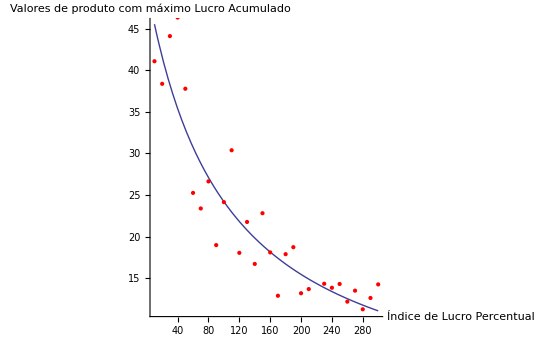

```mathematica
lucro =.;Amp =.;n=.;off=.; (*limpa as variáveis eventualmente ocupadas, Aplitude ou Ganho, Offset e uma constante*)

model = Amp/(n+lucro)+off    (*Modelo de função racional*)
fit=FindFit[ListaValorMaxLucro,model,{Amp,off,n},lucro]
modelf=Function[{lucro},Evaluate[model/.fit]]

Plot[modelf[lucro],{lucro,10,300},
Epilog->{PointSize[Medium],Red,Map[Point,list]},PlotRange->All, AxesOrigin->{0,0},
AxesLabel -> {"Índice de Lucro Percentual","Valores de produto com máximo Lucro Acumulado"}]
```

Função que gera o lucro de acordo com o custo do produto, de modo a maximizar a probabilidade de o produto entrar na região de máximo lucro individual:

```mathematica
lucro[varval_]:=5280.186/(varval+2.076)-100.932
?lucro
```

Global`lucro

lucro[varval_]:=5280.19/(varval+2.076)-100.932